Construction of the phantom. (According to Bronnikov)
The real part of the refractive index is written as:  n(x1,x2,x3) = 1 + f(x1,x2,x3)

The wavelength λ is measured in m :

```mathematica
λ=0.1 10^-6;
<<VectorAnalysis`;
objectfunction[x_List,magn_List,dia_List]:=
Module[{x0=dia[[1]]/3{1,1,1}},
magn[[1]] Boole[Sqrt@DotProduct[x,x]≤ dia[[1]]]
+(magn[[2]]-magn[[1]]) Boole[Sqrt@DotProduct[x-x0,x-x0]≤ dia[[2]]]
+(magn[[3]]-magn[[1]]) Boole[Sqrt@DotProduct[x+x0,x+x0]≤ dia[[3]]]
]
```

Coordinate are measured in microns. The values of the object function are in the range of the value for polystyrene.

```mathematica
objectsizeradius=108/2;
object[x_]:=objectfunction[x,{- 5 10^-7,- 10.5 10^-7,-2 10^-7},{objectsizeradius,18,18}];
```

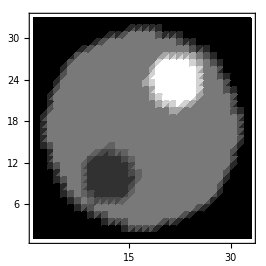

```mathematica
Block[{n=32,range=2.2 objectsizeradius,xx,phi=π/4},
xx={{Cos[phi],-Sin[phi],0},{Sin[phi],Cos[phi],0},{0,0,1}}.{range(-1/2+1/n n1),.2objectsizeradius,range(-1/2+1/n n2)};
ListDensityPlot[
1/(- 10.5 10^-7)Table[object[xx],{n1,0,n},{n2,0,n}],ColorFunction->GrayLevel]
]
```

The wave field downstream  of the object is u[x, y, θ] = Exp[i phase[x, y, θ] - μ[x, y, θ]/2]. Assuming μ = 0 it is given by

```mathematica
downstream[x_,y_,theta_]:=
Exp[ⅈ 2π/λ 
Integrate[
object[{x1,x2,y}]DiracDelta[x-x1 Cos[theta]-x2 Sin[theta]],{x1,-objectsizeradius,objectsizeradius}
,{x2,-objectsizeradius,objectsizeradius}
]
];
```

```mathematica
Block[{theta=π/4,d=objectsizeradius,n=128},
downstreamdata=Table[downstream[x,y,theta],{x,-d,d,d/n},{y,-d,d,d/n}];
]
```

$Aborted

```mathematica
Block[{step=27},
{t,list}=Timing[Table[downstream[x,y,0],{x,-objectsizeradius,objectsizeradius,step},{y,-objectsizeradius,objectsizeradius,step}]];
Print[t];
TableForm[list]
]
```

5.80836

1 | 1 | 1 | 1 | 1
1 | -0.982439-0.186582 ⅈ | -0.568727+0.822526 ⅈ | 0.523365+0.852108 ⅈ | 1
1 | -0.568727+0.822526 ⅈ | 1.+2.74366×10^-13 ⅈ | -0.568727+0.822526 ⅈ | 1
1 | 0.523365+0.852108 ⅈ | -0.568727+0.822526 ⅈ | 0.561067+0.82777 ⅈ | 1
1 | 1 | 1 | 1 | 1

```mathematica
{Options[#],Attributes[#]}&@FourierTransform
```

{{Assumptions:>$Assumptions,GenerateConditions→False,FourierParameters→{0,1}},{Protected,ReadProtected}}

```mathematica
FourierTransform[Exp[ⅈ phase[xxx,yyy,0]],{xxx,yyy},{ξ,η},FourierParameters->{0,2π}]
```

```mathematica
intensity[x_,y_,theta_,z_]:=
Abs[
InverseFourierTransform[
Exp[ⅈ 2π/λ z -ⅈ π λ z(ξ^2+η^2)]FourierTransform[Exp[ⅈ phase[xxx,yyy,theta]],{xxx,yyy},{ξ,η},FourierParameters->{0,2π}]
,{ξ,η},{xx,yy},FourierParameters->{0,2π}
]/.{xx->x,yy->y}
]^2
```